```mathematica
Clear["Global`*"]
```

```mathematica
PacletManager`PacletDirectoryAdd[NotebookDirectory[]];
<< PlotFunctions`
<< SimulationFunctions`
```

```mathematica
ϕ2D =Function[{x,y}, 1/((2^(1+1)π)^(1/4))Exp[-x^2/2] HermiteH[1, x] Exp[-y^2/2] HermiteH[1, y] Exp[2 ⅈ x^2 + y ⅈ]];
ϕ2D =Function[{x,y}, 1/((2^(1+1)π)^(1/4))Exp[-x^2/2] HermiteH[1, x] Exp[-y^2/2] HermiteH[1, y]];
ϕ2D = Function[{x,y}, Exp[-(x-2)^2-(y-1)^2]];
V2D = Function[{x, y}, 1/2(x^2+y^2)];
```

```mathematica
Exp[2]
```

ⅇ^2

```mathematica
ShowRawEvolution[
	ϕ2D, V2D, {-5, 5}, {-5, 5}, 1, 
	PlotDomain -> {{-2.5 + .5, 2.5 + .5}, {-2.5 + .5,2.5 + .5}},
	PlotRange -> {0, 0.35},
	PotentialTransform -> (#/8&),
	PointsActivePassive -> {10, 50},
	TimeSteps -> True
]
```

simulating  3.32313

animating  0.0020364

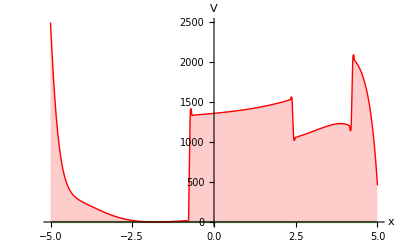
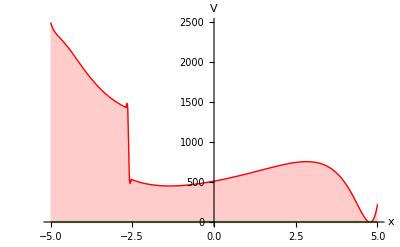
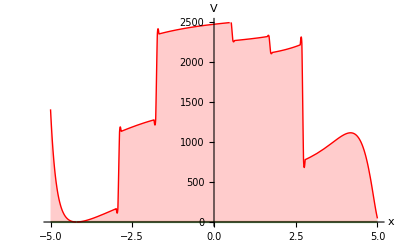
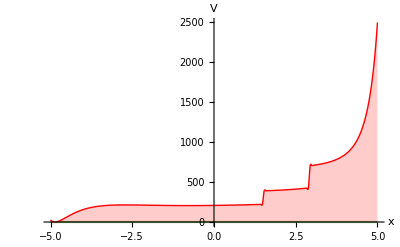
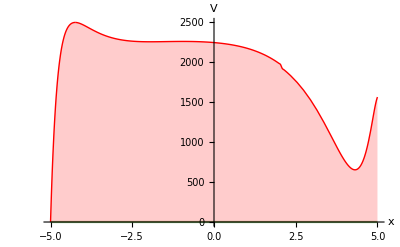
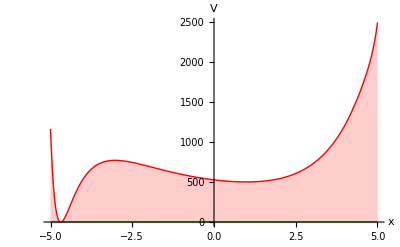
```mathematica
GraphicsGrid[{{-Graphics-, -Graphics-},{  -Graphics-,-Graphics-},{-Graphics-,-Graphics-}}, Frame -> All, ImageSize->{.5 10^3,.5 10^3}]
```